# 1.4

```mathematica
OTCdata={11.88,6.27,5.49,4.81,4.40,3.78,3.44,3.11,2.88,2.68,7.99,6.07,5.26,4.79,4.05,3.69,3.36,3.03,2.74,2.63,7.15,5.98,5.07
,4.55,3.94,3.62,3.26,2.99,2.74,2.62,7.13,5.91,4.94,4.43,3.93,3.48,3.20,2.89,2.69,2.61};
```

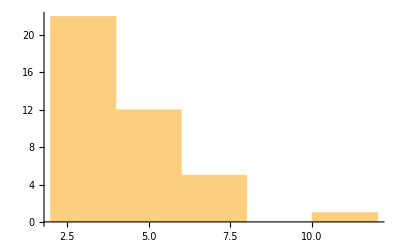

```mathematica
Histogram[OTCdata]
```

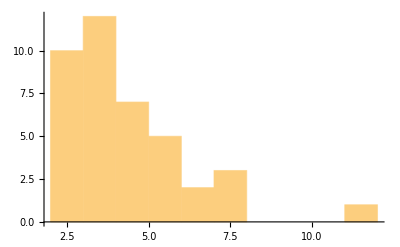

```mathematica
Histogram[OTCdata,"Sturges"]
```

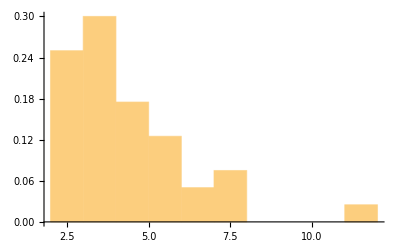

```mathematica
Histogram[OTCdata,"Sturges","Probability"]
```

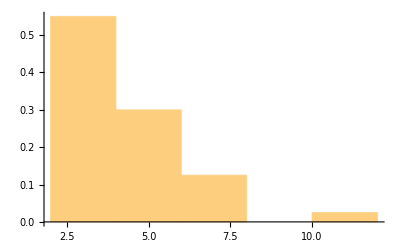

```mathematica
Histogram[OTCdata,Automatic,"Probability"]
```

```mathematica
Select[#>4&][OTCdata]
```

{11.88,6.27,5.49,4.81,4.4,7.99,6.07,5.26,4.79,4.05,7.15,5.98,5.07,4.55,7.13,5.91,4.94,4.43}

```mathematica
Length[Select[#>4&][OTCdata]]/Length[OTCdata]
```

9/20

```mathematica
N[Length[Select[#>4&][OTCdata]]/Length[OTCdata]]
```

0.45

```mathematica
Probability[x<5,x\[Distributed]OTCdata]
```

29/40

```mathematica
N[Probability[x<5,x\[Distributed]OTCdata]]
```

0.725